# Zestaw 5

## Zadanie 1. Oscylator harmoniczny, DSolve, PlotLegends

Rozwiąż równanie ruchu dla klocka o masie 𝑚 przymocowanego do sprężyny o stałej sprężystości 𝑘. Ruch odbywa się bez tarcia powierzchniowego.

```mathematica
OscillatorEquasion := m x''[t] == -k x[t]
```

Skorzystaj z polecenia DSolve:

### 1) Znajdź ogólną postać rozwiązania x[t] dla równania

```mathematica
DSolve[OscillatorEquasion]
```

{{x[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

Od ilu stałych zależy rozwiązanie tego równania?
Odp: 2

Podstaw za te stałe wybrane nie-zerowe wartości

```mathematica
OscillatorEquasionWithArgs[m_, k_] := m x''[t] == -k x[t];
m0 = 2;
k0 = 3;
DSolve[OscillatorEquasionWithArgs[m0, k0]]
```

{{x[t]→C[1] Cos[√(3/2) t]+C[2] Sin[√(3/2) t]}}

### 2) Zadaj warunki początkowe jednoznacznie określające rozwiązanie x[t] dla równania

Ponownie rozwiąż z użyciem DSolve.
Użyj oznaczeń: prędkość początkowa = v0, położenie początkowe = x0.

```mathematica
solution = DSolve[{OscillatorEquasion, x[0] == x0, x'[0] == v0}, x, t]
```

{{x→Function[{t},(√k x0 Cos[(√k t)/(√m)]+√m v0 Sin[(√k t)/(√m)])/(√k)]}}

### 3) Rozwiązanie z 2) wykorzystaj do zdefiniowania funkcji fx[t, m] pokazującej położenie klocka po czasie

Rozwiązanie z 2) wykorzystaj do zdefiniowania funkcji f[t, m] pokazującej położenie klocka po czasie  dla ustalonych , , oraz , ale dowolnej masy .
Przedstaw położenie klocków o masach odpowiednio , ,  na wykresie dla  od  do .

```mathematica
fxBase[t1_][m_, k_, x0_, v0_] := Module[{solution},
solution = DSolve[
{m x''[t] == -k x[t], x[0] == x0, x'[0] == v0},
x, t
];
Last[First @ Flatten @ solution][t1]
]

fx[t_, m_] = Module[{k, x0, v0},
x0 = 1;
v0 = 0;
k = 1;
fxBase[t][m, k, x0, v0]
]
```

Cos[t/(√m)]

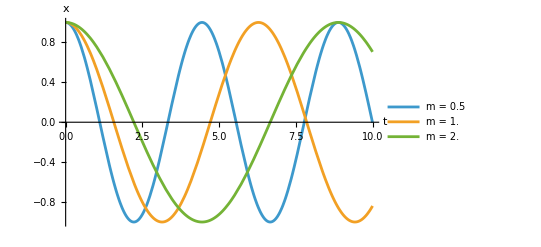

```mathematica
masses = {1/2, 1, 2};

xFunctions = Map[
m |-> fx[t,  m],
masses
];

Plot[
xFunctions,
{t, 0, 10},
AxesLabel -> {"t", "x"},
PlotLegends-> Map[m |-> "m = " <> ToString[N[m]], masses]
]
```

### 4) Podobnie do 3) zdefiniuj funkcję fv[t, m] pokazującą prędkość klocka po czasie

Podobnie do 3) zdefiniuj funkcję  fv[t, m] pokazującą prędkość klocka po czasie  dla ustalonych , , oraz , ale dowolnej masy .

```mathematica
fvBase[t_][m_, k_, x0_, v0_] := D[fxBase[t][m, k, x0, v0], t];

fv[t_, m_] = Module[{k, x0, v0},
x0 = 1;
v0 = 0;
k = 1;
fvBase[t][m, k, x0, v0]
]
```

-Sin[t/(√m)]/(√m)

Wykonaj analogiczny wykres jak w 3) pokazujący prędkość klocka dla różnych mas.

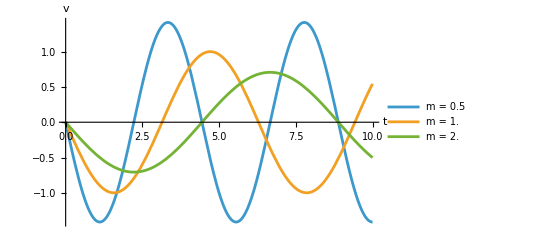

```mathematica
vFunctions = Map[
m |-> fv[t,  m],
masses
];

Plot[
vFunctions,
{t, 0, 10},
AxesLabel -> {"t", "v"},
PlotLegends-> Map[m |-> "m = " <> ToString[N[m]], masses]
]
```

### 5) Jaki jest okres wykonywanych drgań dla klocków o powyższych masach?

```mathematica
initialPositions = Flatten[Map[
m |-> Solve[fx[t, m] == 1, t, Reals],
masses
]]
```

{t→ConditionalExpression[√2 π C[1], C[1]∈ℤ],t→ConditionalExpression[2 π C[1], C[1]∈ℤ],t→ConditionalExpression[2 √2 π C[1], C[1]∈ℤ]}

```mathematica
periods = Map[
p |-> First[Last[p]] / C[1],
initialPositions
]
```

{√2 π,2 π,2 √2 π}

### 6) Sprawdź, bez podstawiania wartości za , , , , czy w trakcie ruch klocka zachowana jest suma energii potencjalnej i kinetycznej

```mathematica
KineticEnergy[t_] = m fvBase[t][m, k, x0, v0]^2 / 2
```

(m (√k v0 Cos[(√k t)/(√m)]-(k x0 Sin[(√k t)/(√m)])/(√m))^2)/(2 k)

```mathematica
PotentialEnergy[t_] = k fxBase[t][m, k, x0, v0]^2 / 2
```

1/2 (√k x0 Cos[(√k t)/(√m)]+√m v0 Sin[(√k t)/(√m)])^2

```mathematica
FullSimplify[KineticEnergy[t] + PotentialEnergy[t]]
```

1/2 (m v0^2+k x0^2)

## Zadanie 2. Oscylator harmoniczny tłumiony, DSolve, ParametricPlot

Rozwiąż równanie ruchu dla klocka o masie  przymocowanego do sprężyny o stałej sprężystości  przy założeniu, że opory ruchu są proporcjonalne do prędkości klocka ze współczynnikiem .

Skorzystaj z polecenia DSolve:

### 1) Zadaj warunki początkowe jednoznacznie określające rozwiązanie x[t] dla równania

Użyj oznaczeń prędkość początkowa = v0 oraz położenie początkowe = x0.

```mathematica
DSolve[{
m x''[t] == -b x'[t] - k x[t],
x[0] == x0,
x'[0] == y0
}, x, t]
```

{{x→Function[{t},(-b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) x0+b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) x0+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) √(b^2-4 k m) x0+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) √(b^2-4 k m) x0-2 ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m y0+2 ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m y0)/(2 √(b^2-4 k m))]}}

### 2) Rozwiązanie z 1) wykorzystaj do zdefiniowania funkcji f[t, m, b] pokazującej położenie klocka po czasie

Rozwiązanie z 1) wykorzystaj do zdefiniowania funkcji f[t, m, b] pokazującej położenie klocka po czasie  dla ustalonych , , oraz , ale dowolnej masy  oraz współczynnika oporu .

```mathematica
fBase[t1_][m_, k_, b_, x0_, v0_] := Module[{solution},
solution = DSolve[
{
m x''[t] == -b x'[t] - k x[t],
x[0] == x0,
x'[0] == v0
},
x, t];
Last[First[Flatten[solution]]][t1]
];

f[t_, m_, b_] = Module[{k, x0, v0},
x0 = 1;
v0 = 0;
k = 1;
fBase[t][m, k, b, x0, v0]
]
```

(-b ⅇ^(1/2 (-b/m-(√(b^2-4 m))/m) t)+b ⅇ^(1/2 (-b/m+(√(b^2-4 m))/m) t)+ⅇ^(1/2 (-b/m-(√(b^2-4 m))/m) t) √(b^2-4 m)+ⅇ^(1/2 (-b/m+(√(b^2-4 m))/m) t) √(b^2-4 m))/(2 √(b^2-4 m))

Przedstaw położenie klocka o masie  oraz wartościach:
 (bez tłumienia), , , , 
na wykresie dla  od 0 do 20. Użyj Plot.

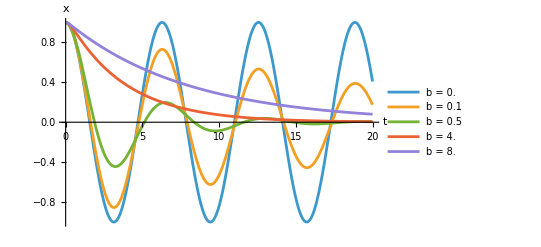

```mathematica
bValues = {0, 1/10, 1/2, 4, 8};

PlotBFunctions[bValues_, tMin_, tMax_] := Module[{bFunctions},
bFunctions = Map[
b |-> f[t,  1, b],
bValues
];

Plot[
bFunctions,
{t, tMin, tMax},
AxesLabel -> {"t", "x"},
PlotLegends-> Map[b |-> "b = " <> ToString[N[b]], bValues]
]
];

PlotBFunctions[bValues, 0, 20]
```

### 3) Wykonaj wykres fazowy dla oraz wartości jak w punkcie 2)

W tym przypadku wykres fazowy to  zależność prędkości od położenia  klocka.

```mathematica
fvbBase[t_][m_, k_, b_, x0_, v0_] := D[fBase[t][m, k, b, x0, v0], t];

fvb[t_, m_, b_] = Module[{k, x0, v0},
k = 1;
x0 = 1;
v0 = 0;
fvbBase[t][m, k, b, x0, v0]
];
```

Możesz użyć funkcji ParametricPlot  by narysować krzywe  dla odpowiednio dużego .

```mathematica
?ParametricPlot
```

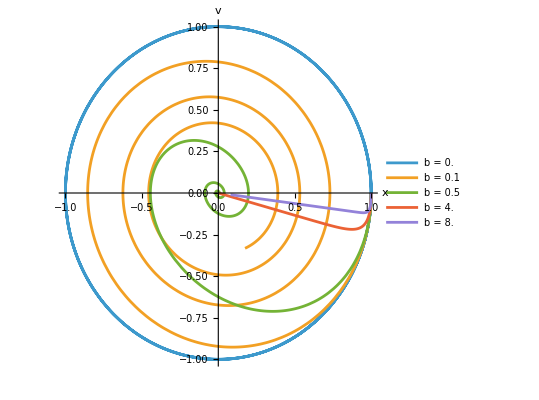

```mathematica
mass = 1;
paramFunctions = Map[
b |-> {f[t, mass, b], fvb[t, mass, b]},
bValues
];

ParametricPlot[
paramFunctions,
{t, 0 , 20},
AxesLabel -> {"x", "v"},
PlotLegends-> Map[b |-> "b = " <> ToString[N[b]], bValues]
]
```

### 4) Dla jakiej wartości współczynnika tłumienia zmienia się jakościowy charakter ruchu?

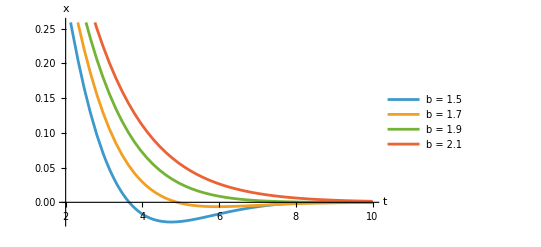

```mathematica
PlotBFunctions[{1.5,1.7, 1.9, 2.1}, 2, 10]
```

Odp:

- Brak tłumienia

- Ruch harmoniczny tłumiony - Tłumienie podkrytyczne

- Tłumienie krytyczne

- Ruch opóźniony (“bloczek opadający w oleju”) - Tłumienie nadkrytyczne

### 5) Przedstaw na wykresie sumę energii potencjalnej i kinetycznej klocka

Przedstaw na wykresie sumę energii potencjalnej i kinetycznej klocka dla , , , , oraz zmieniającego się tłumienia .

```mathematica
PotentialEnergy[t_, m_, k_, b_, x0_, v0_] = k fBase[t][m, k, b, x0, v0]^2 / 2;
KineticEnergy[t_, m_, k_, b_, x0_, v0_] = m fvbBase[t][m, k, b, x0, v0]^2 / 2;

MechanicalEnergy[t_, m_, k_, b_, x0_, v0_] = PotentialEnergy[t, m, k, b, x0, v0] + KineticEnergy[t, m, k, b, x0, v0];
```

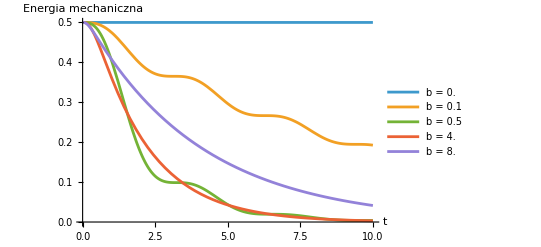

```mathematica
PlotEnergy := Module[{m, k, x0, v0, bValues, totalEnergyFunctions},
m = 1;
k = 1;
x0 = 1;
v0 = 0;
bValues = {0, 1/10, 1/2, 4, 8};

mechanicalEnergyFunctions = Map[
b |-> MechanicalEnergy[t, m, k, b, x0, v0],
bValues
];

Plot[
mechanicalEnergyFunctions,
{t, 0, 10},
AxesLabel -> {"t", "Energia mechaniczna"},
PlotLegends-> Map[b |-> "b = " <> ToString[N[b]], bValues]
]
]

PlotEnergy
```

Czy energia jest zachowana?
Odp: Nie

## Zadanie 3. Przybliżenie małych drgań, Series, Show, PlotRange, PlotLegends

W przypadku wahadła matematycznego złożonego z małej kulki o masie  zawieszonej na nitce o długości , energię potencjalną kulki można wyrazić jako 
gdzie:

- wysokość kulki nad położeniem równowagi,

- kąt  wychylenia  wahadła,

- przyspieszenie  grawitacyjne

Dla małych kątów , można przybliżyć 
Podobnie dla małych kątów , można przybliżyć  , skąd:

gdzie .
W zadaniu 1 okres drgań wynosił .
Z kolei  dla wahadła matematycznego po podstawieniu za  wartości  otrzymamy dobrze znany wynik .

Takie podejście można zastosować do bardzo wielu układów, w których ruch odbywa się w potencjale kwadratowym albo potencjał można przybliżyć przez potencjał kwadratowy.

W tym zadaniu sprawdź w jakim stopniu funkcję  można przybliżyć korzystając z rozwinięcia w szereg Taylora względem punktu .

```mathematica
Clear[f];
f[theta_] := 1 - Cos[theta];
theta0 = 0;
```

W tym celu:

### 1) Rozwiń do 10-stopnia względem korzystając z funkcji Series

```mathematica
?Series
```

```mathematica
Series[f[theta], {theta, theta0, 10}]
```

theta^2/2-theta^4/24+theta^6/720-theta^8/40320+theta^10/3628800+O[theta]^11

### 2) Przedstaw na wykresie funkcję

Przedstaw na wykresie funkcję  w zakresie od   do  , ogranicz z użyciem PlotRange zakres wartości  do .
Na potrzeby kolejnego punktu, niech funkcja będzie częściowo przezroczysta, użyj PlotStyle -> {Opacity[0.5, Black]}.

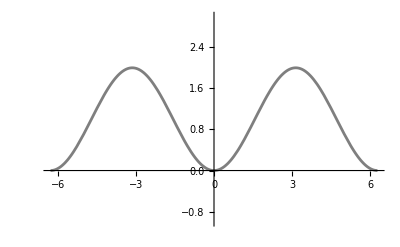

```mathematica
thetaRange = {theta, -2 Pi, 2 Pi};

plot = Plot[
f[theta],
thetaRange,
PlotRange -> {-1, 3},
PlotStyle -> {Opacity[0.5, Black]}
]
```

### 3) Przedstaw przybliżenia funkcji na powyższym wykresie

Wystarczą tylko parzyste stopnie, dlaczego? 
Niech przybliżenia będą wyrysowane linią przerywaną. Wygodnie użyć funkcji Show.

```mathematica
degrees = Range[2, 10, 2];

DegreeToFunction[degree_] := Module[{g},
g[t_] = Normal[Series[f[t], {t, theta0, degree}]];
g
];

aproxFunctions = Map[
degree |-> DegreeToFunction[degree],
degrees
];

aproxPlot = Plot[
Evaluate[Map[
function |-> function[theta],
functions
]],
thetaRange
];

Show[plot, aproxPlot]
```

-Graphics-

### 4) Dodaj legendę do wykresu korzystając z opcji PlotLegends -> "Expressions"

```mathematica
aproxPlot = Plot[
Evaluate[Map[
function |-> function[theta],
functions
]],
thetaRange,
PlotLegends-> "Expressions"
];

Show[plot, aproxPlot]
```

-Graphics-

### 5) Zbadaj jaka jest różnica oraz przybliżeń kolejnych stopni w punkcie

```mathematica
theta1 = Pi / 2;

CalculateError[degree_] := Module[{AproxFunction, error},
AproxFunction[t_] = Normal[Series[f[t], {t, theta0, degree}]];
error = N @ Abs[
(AproxFunction[theta1] - f[theta1]) / f[theta1]
];
error
]

Map[
degree |->  degree -> PercentForm @ CalculateError[degree],
degrees
]
```

{2→23.37%,4→1.997%,6→0.08945%,8→0.002474%,10→0.00004648%}

Dla jakiego stopnia przybliżenia różnica ta jest mniejsza od 1%?

```mathematica
closeEnough = False;
n = 0;
result = {};

While[!closeEnough,
n += 2;
AproxFunction[t_] = Normal[Series[f[t], {t, theta0, n}]];
error = CalculateError[n];

closeEnough = error < 0.01;
]

Print["Stopień: " <> ToString[n]]
Print["Błąd: " <> ToString @ PercentForm[error]]
```

Stopień: 6

Błąd: 0.08945%